## The idea behind t test (compiled in javascript and mathematica)

Ning Xu, Pierre de Moral

### Basics of t distribution

(1) t distribution is the distribution of the sample mean, whose sample is drawn randomly from a normal - distributed population.
(2) standard t distribution is uniquely defined by its degree of freedom (one degree of freedom is mapped to only one t distribution)
(3) t distribution is heavy-tail distribution, whose tail is slightly heavier than normal distribution. (As degree of freedom increasing, t distribution will be infinitely similar to normal distribution, see the following graph)
	refer to the discussion of “heavy tail and outliers discussion” in tut 2

Graph 1 : degree of freedom of t distribution
blue     : d.f. = 1
yellow : d.f. = 2
green   : d.f. = 5

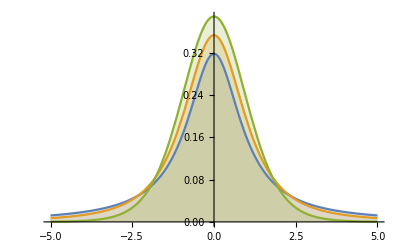

### A demonstration app of t statistic and its p value

You can choose one of the potential 3 hypothesis from the top

You can control the parameters of the t test on the left panel

n is the sample size of your sample

μ_0 is the hypothetical mean you propose for the population

α is the significant level of your test

σ^2 is the population variance

(You can ignore this parameter, but for the die-hard fans of statistics....) seed is the random number seed of random sampling from a normal distributed population (computer can only generate pseudo - random numbers, google random seed for detail)

test statistic, cutoff point, p - value and conclusion are reported

Black bar is the cutoff point;

Red bar is the test statistic;

Dark purple area is the rejection region of H_0

Area of Dark purple  + Area of light purple = p-value

Decision based on rejection region : If test stat falls into the rejection region, reject H_0; otherwise do not reject H_0

Decision based on p-value : If p-value is larger than α , do not reject H_0; otherwise reject H_0